```mathematica
data={1.05,1.01,0.97,1.14,0.92,0.99,1.07};
Min[data]
```

0.92

```mathematica
Max[data]
```

1.14

```mathematica
Total[data]
```

7.15

```mathematica
Mean[data]
```

1.02143

```mathematica
Median[data]
```

1.01

```mathematica
(* 中位数 middle value *)
```

```mathematica
(* {Subscript[x, i]} N values;
mean: <x>=(Σ_i Subscript[x, i])/N;
variance: σ^2=(Σ_i(Subscript[x, i]-<x>)^2)/(N-1);
standard deviation: σ *)
Variance[data]
```

0.00521429

```mathematica
StandardDeviation[data]
```

0.07221

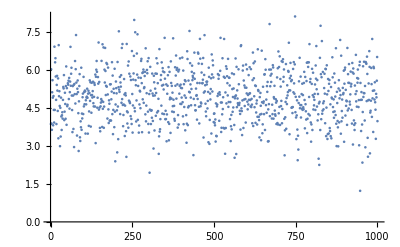

```mathematica
inputdata=Import["https://eee.uci.edu/12f/40330/lesson4.dat"];
ListPlot[inputdata]
```

```mathematica
data2=inputdata[[All,2]];
```

```mathematica
Mean[data2]
```

4.98317

```mathematica
StandardDeviation[data2]
```

1.01038

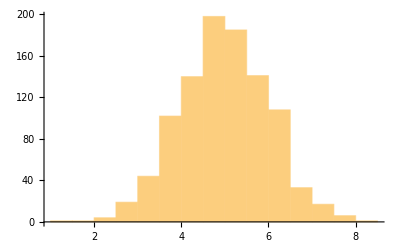

```mathematica
Histogram[data2]
```

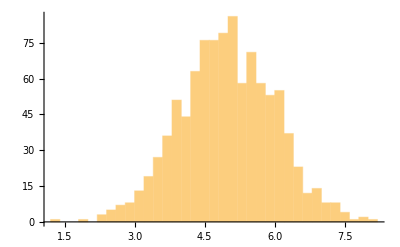

```mathematica
(* histogram 直方图 ；
改变组数如下 *)
Histogram[data2,40] (* 40组 *)
```

```mathematica
Histogram[data2,{0.2}] (* 组距0.2 *)
```

-Graphics-

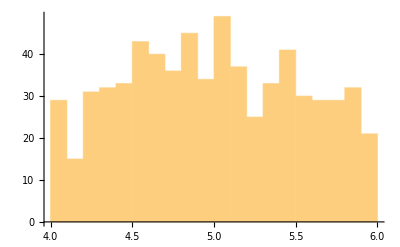

```mathematica
Histogram[data2,{4,6,0.1}](* 4~6，组距0.1 *)
```

```mathematica
(* probability density fctn: P(x);
P(x)dx=prob. that a value lies b/w x & x+dx;
b/w means between *)
```

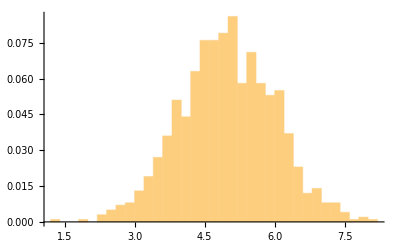

```mathematica
Histogram[data2,{0.2},"Probability"]
```

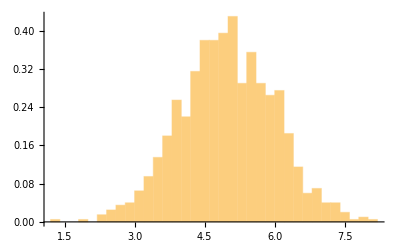

```mathematica
Histogram[data2,{0.2},"ProbabilityDensity"]
```

```mathematica
list={a,b,c};
Permutations[list]
```

{{a,b,c},{a,c,b},{b,a,c},{b,c,a},{c,a,b},{c,b,a}}

```mathematica
Factorial[3]
```

6

```mathematica
list2={a,b,c,d,e};
Length[Permutations[list2]]
```

120

```mathematica
Binomial[4,3](* Subscript[C, 4]^3 *)
```

4